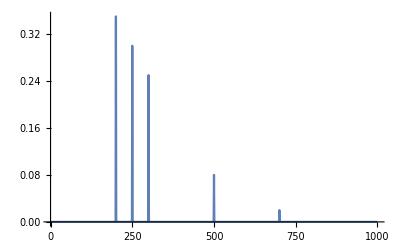

```mathematica
data={200,250,300,500,700};
A=EmpiricalDistribution[{35,30, 25,8,2}->data];
DiscretePlot[PDF[A,x],{x,0,1000},Joined->True]
```

```mathematica
vec=RandomVariate[A,100]
```

{250,300,250,250,300,200,250,200,300,200,300,200,250,200,500,200,200,250,300,200,300,250,700,300,200,250,250,300,300,250,700,200,500,250,200,250,500,250,500,300,300,250,500,250,250,300,250,300,250,300,200,250,300,200,200,200,250,250,250,500,250,250,300,200,250,200,200,200,250,250,200,200,200,200,250,300,300,250,250,300,250,300,200,500,300,300,250,250,250,200,200,250,200,250,300,200,500,200,200,250}

```mathematica
DiscretePlot[PDF[EmpiricalDistribution[vec],x],{x,0,1000},Joined->True]
```

7.01856

-Graphics-

{{0.43866,0.43866},{0.43866,1.31598},{0.43866,2.1933},{0.43866,3.07062},{0.43866,3.94794},{0.43866,4.82526},{0.43866,5.70258},{0.43866,6.5799},{1.31598,0.43866},{1.31598,1.31598},{1.31598,2.1933},{1.31598,3.07062},{1.31598,3.94794},{1.31598,4.82526},{1.31598,5.70258},{1.31598,6.5799},{2.1933,0.43866},{2.1933,1.31598},{2.1933,2.1933},{2.1933,3.07062},{2.1933,3.94794},{2.1933,4.82526},{2.1933,5.70258},{2.1933,6.5799},{3.07062,0.43866},{3.07062,1.31598},{3.07062,2.1933},{3.07062,3.07062},{3.07062,3.94794},{3.07062,4.82526},{3.07062,5.70258},{3.07062,6.5799},{3.94794,0.43866},{3.94794,1.31598},{3.94794,2.1933},{3.94794,3.07062},{3.94794,3.94794},{3.94794,4.82526},{3.94794,5.70258},{3.94794,6.5799},{4.82526,0.43866},{4.82526,1.31598},{4.82526,2.1933},{4.82526,3.07062},{4.82526,3.94794},{4.82526,4.82526},{4.82526,5.70258},{4.82526,6.5799},{5.70258,0.43866},{5.70258,1.31598},{5.70258,2.1933},{5.70258,3.07062},{5.70258,3.94794},{5.70258,4.82526},{5.70258,5.70258},{5.70258,6.5799},{6.5799,0.43866},{6.5799,1.31598},{6.5799,2.1933},{6.5799,3.07062},{6.5799,3.94794},{6.5799,4.82526},{6.5799,5.70258},{6.5799,6.5799}}

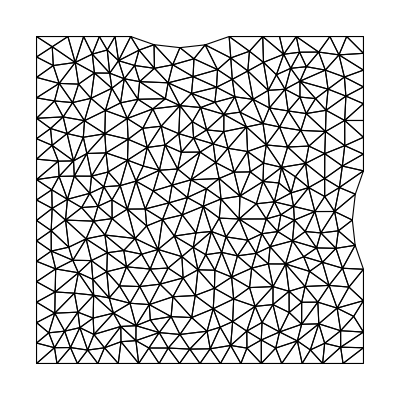

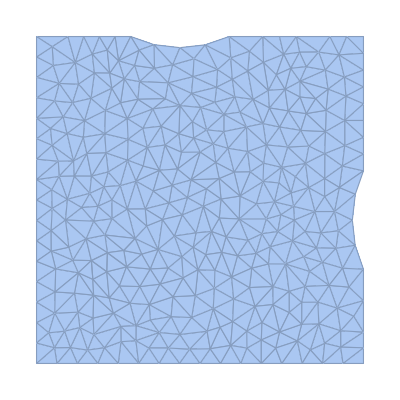

{5.70258,3.07062}

{5.70258,3.94794}

BooleanRegion[#1||#2&,{Disk[{5.70258,3.07062},{0.35,0.35}],Disk[{5.70258,3.94794},{0.35,0.35}]}]

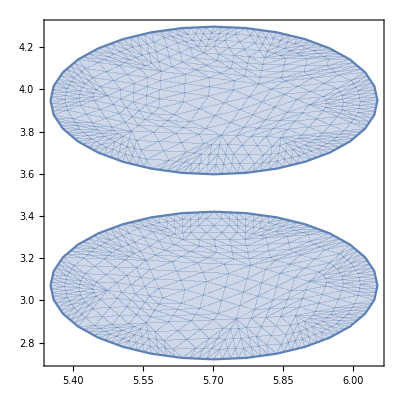

64

```mathematica
<<AceGen`;
<<AceFEM`;
L=1.2; (*valore test*)
Dc=0.700;
Rc=Dc/2;
Nincl=64;(* tiene conto che i due spazi estremali sono la metà*)
Ninclx=Sqrt[Nincl];
Nincly=Sqrt[Nincl];
volfrac=0.5;
inctot=Ninclx Nincly;
Ainc=Pi*Rc^2;
AT=Ainc *inctot/volfrac;
L=Sqrt[AT]
Lx = L; 
Ly = L; 
diameter={200,250,300,500,700};
distribution=EmpiricalDistribution[{35,30, 25,8,2}->diameter];
Print[DiscretePlot[PDF[distribution,x],{x,0,1000},Joined->True]];
Rcvec=RandomVariate[distribution,Nincl];
Rcvec=N[Rcvec/(2*1000),2];
xc=Lx/2;
yc=Ly/2;
Δx=(Lx-Dc Ninclx)/Ninclx;
Δy=(Ly-Dc Ninclx)/Ninclx;
firstxc=xc-(Δx/2)-Rc-(-1+Ninclx/2)(Dc+Δx);
firstyc=yc-(Δy/2)-Rc-(-1+Nincly/2)(Dc+Δy);
centerx=Table[firstxc+(i-1)(Dc+Δx),{i,1,Ninclx}];
centery=Table[firstyc+(i-1)(Dc+Δx),{i,1,Ninclx}];
tempcenter=Table[{centerx⟦i⟧,centery⟦j⟧},{i,1,Ninclx},{j,1,Nincly}];
tempcenter=Flatten[tempcenter,1]
Ωext=Rectangle[{0,0},{Lx,Ly}];
Ω=Ωext;

Do[
(*Ω=RegionDifference[Ω,Disk[tempcenter⟦i⟧, {Rcvec⟦i⟧,Rcvec⟦i⟧}]]*)
Ω=RegionDifference[Ω,Disk[tempcenter⟦i⟧, {0.7/2,0.7/2}]];
(*ATTENZIONE: variando i due raggi non è rispettata più la vol frac*)
,{i,1,52}];
(*RegionPlot[Ω]*)
Ω=RegionDifference[Ω,Disk[tempcenter⟦53⟧, {0.7/2,0.7/2}]]; (* ?????? *)
marker={{{Lx/100,Ly/100},1}};
Do[
marker=Join[marker,{{tempcenter⟦i⟧,2}}]
,{i,1,Nincl}];

(*RegionPlot[Ω]*)
mesh=ToElementMesh[Ω,"RegionHoles"->None,"MeshOrder"->1];
%["Wireframe"]
MeshRegion[mesh]
```

2.0022

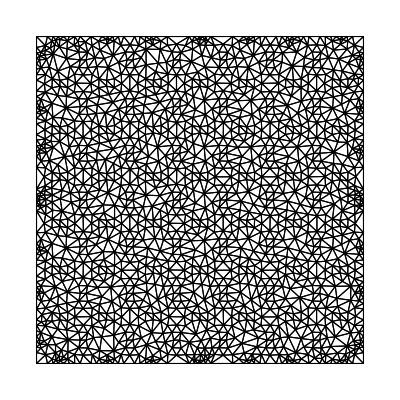

```mathematica
L=1.2; (*valore test*)
Dc=0.250;
Rc=Dc/2;
Nincl=49;(* tiene conto che i due spazi estremali sono la metà*)
Ninclx=Sqrt[Nincl];
Nincly=Sqrt[Nincl];
volfrac=0.6;
inctot=Ninclx Nincly;
Ainc=Pi*Rc^2;
AT=Ainc *inctot/volfrac;
L=Sqrt[AT]
Lx = L; 
Ly = L; 
xc=Lx/2;
yc=Ly/2;
Δx=(Lx-Dc Ninclx)/Ninclx;
Δy=(Ly-Dc Ninclx)/Ninclx;
firstxc=xc-(Δx/2)-Rc-(-1+Ninclx/2)(Dc+Δx);
firstyc=yc-(Δy/2)-Rc-(-1+Nincly/2)(Dc+Δy);
centerx=Table[firstxc+(i-1)(Dc+Δx),{i,1,Ninclx}];
centery=Table[firstyc+(i-1)(Dc+Δx),{i,1,Ninclx}];

Ωext=Rectangle[{0,0},{Lx,Ly}];
Ω=Ωext;
Do[
Ω=RegionDifference[Ω,Disk[{centerx⟦i⟧,centery⟦j⟧}, {Rc,Rc}]](*ATTENZIONE: variando i due raggi non è rispettata più la vol frac*)
,{i,1,Ninclx},{j,1,Nincly}];

marker={{{Lx/100,Ly/100},1}};
Do[
marker=Join[marker,{{{centerx⟦i⟧,centery⟦j⟧},2}}]
,{i,1,Ninclx},{j,1,Nincly}];
(*RegionPlot[Ω]*)
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1];
(*mesh=ToElementMesh[Ωext,"MeshOrder"->1,"RegionMarker"->{{{Lx/100,Ly/100},1}},"MeshElementType"->TriangleElement,"MaxCellMeasure"->0.01];
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1];*)
%["Wireframe"]
```

```mathematica
Ωext=Rectangle[{0,0},{Lx,Ly}]
Ω=RegionDifference[Ω,Disk[tempcenter⟦1⟧, {Rcvec⟦1⟧,Rcvec⟦1⟧}]]
Disk[tempcenter⟦1⟧, {Rcvec⟦1⟧,Rcvec⟦1⟧}]
```

Rectangle[{0,0},{7.41471,7.41471}]

EmptyRegion[2]

Disk[{0.370735,0.370735},{200,200}]